```mathematica
dataMathews=Import[NotebookDirectory[]<>"data/Matthews 2023 - Fig 5A-Untreated-ETRmax.csv"];
```

```mathematica
gauss=a ⅇ^(-((x-b)/c)^2);
```

```mathematica
fitMatthews=FindFit[ToExpression@dataMathews[[3;;-1]],{gauss,a>200,c>0,b>20},{a,b,c},x]
```

{a→226.682,b→28.142,c→14.0864}

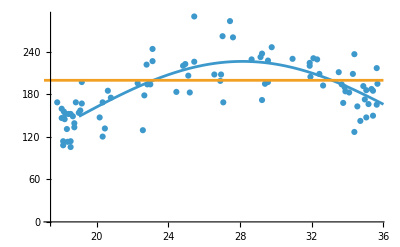

```mathematica
Show[{
ListPlot[ToExpression@dataMathews[[3;;-1]]],
Plot[{gauss/.fitMatthews,200},{x,17,36}]}]
```